```mathematica
SetDirectory[NotebookDirectory[]]
relevant=Select[Union[Import["/Users/hayssam/Documents/ISOP_0.2/tests/relevant_documents.tsv"]],#[[4]]=="False"&];
relevant=Select[relevant,Length[#]==75&];
bySeed=GatherBy[relevant,#[[7]]&];
Length[relevant]
```

/Users/hayssam/Documents/ISOP_0.2/tests

4562

```mathematica
Union[relevant[[All,{1,2,3,4,8,9}]]]//MatrixForm
nMethods=Length[%]
```

(True | False | True | False | LSI | 500
True | False | True | False | XAP | 100)

2

```mathematica
pathways=Union[relevant[[All,5]]]
```

{2,4,7,9,11,14}

```mathematica
RowMethod[row_]:=row[[{8,9,1,2,3,4}]]
Offsets[row_]:= row[[Range[10,Length[row],3]]]
Precisions[row_]:= row[[Range[11,Length[row],3]]]
Recalls[row_]:= row[[Range[12,Length[row],3]]]
Pathway[row_]:=row[[5]]
QuerySize[row_]:=row[[6]]
PrecPlot[row_]:=ListLinePlot[Partition[Riffle[Offsets[row],Precisions[row]],2]]
RecallPlot[row_]:=ListLinePlot[Partition[Riffle[Offsets[row],Recalls[row]],2],PlotRange->{{0,1100},{0,1.1}},PlotStyle->If[row[[8]]=="LSI",{Black},{Red}]]
PrecRecallPlot[row_]:=
ListLinePlot[Partition[Riffle[Recalls[row],Precisions[row]],2],PlotRange->{{0,1.1},{0,1.1}},PlotStyle->If[row[[8]]=="LSI",{Black},{Red}]]
```

```mathematica
pw=7;
querySizes=Union[Select[relevant,#[[5]]==pw&][[All,6]]]
```

{1,2,5,10,13,27,68,102}

```mathematica
DistribPrecForPwSize[pw_,querySize_]:=With[{thisRelevant=GatherBy[Select[relevant,(#[[5]]==pw) ∧ (#[[6]]==querySize)&],RowMethod]},
#[[1,{6,8,9,1,2,3}]]->#[[All,20]]&/@thisRelevant
]
DistribRecForPwSize[pw_,querySize_]:=With[{thisRelevant=GatherBy[Select[relevant,(#[[5]]==pw) ∧ (#[[6]]==querySize)&],RowMethod]},
#[[1,{6,8,9,1,2,3}]]->#[[All,21]]&/@thisRelevant
]
```

```mathematica
TagForMethods[m_]:= 
Style[Grid[Transpose[{{m[[1]], m[[2]], m[[3]]}, {Switch[m[[4]],"False","",-1,"G+","True","G",_,"G"<>ToString[m[[4]]]], If[m[[5]]=="True","M",""], If[m[[6]]=="True","S",""]}}],Frame->LightGray],FontSize->8]
TagForMethods[{1,"LSI",250,"True","True","True"}]
```

1 | G
LSI | M
250 | S

## Box / whiskers

```mathematica
pw=7;
val=DistribRecForPwSize;
d=Join[
val[pw,1],
val[pw,2],
val[pw,5],
val[pw,querySizes[[-3]]],
val[pw,querySizes[[-1]]]
];
d=Sort[d];
```

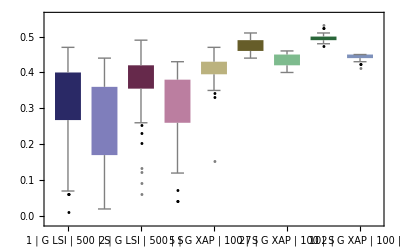

```mathematica
BoxWhiskerChart[
d[[All,2]],"Outliers",
ChartStyle->
Table[
If[d[[i,1,2]]=="XAP",
Lighter[ColorData[1,"ColorList"][[Floor[(i-1)/(nMethods)]+1]]],
Darker[ColorData[1,"ColorList"][[Floor[(i-1)/(nMethods)]+1]]]
],{i,1,Length[d]}],
ChartLabels->(TagForMethods[#[[1]]]&/@ d),
PlotRange->{Automatic,Automatic},
ImageSize->Full]
```

## Average precision

```mathematica
Ap[r_]:= With[{parts=Partition[r[[10;;]],3]},
With[{recall=parts[[All,3]],prec=parts[[All,2]]},
Total[Prepend[Differences[recall],recall⟦1⟧]*prec]
]
]
```

```mathematica
byMethod=GatherBy [relevant,#[[{8,9,1,2,3}]]&];
apByMethod={#[[1,{8,9,1,2,3}]],Ap /@ #}& /@ byMethod;
apByMethod=Sort[apByMethod];
```

```mathematica
Dimensions[apByMethod]
```

{2,2}

```mathematica
apByMethod[[All,1]]//MatrixForm
```

(LSI | 500 | True | False | True
XAP | 100 | True | False | True)

```mathematica
SortBy[{#[[1]],Mean[#[[2]]]}&/@ apByMethod,#[[2]]&]//MatrixForm
```

({XAP,100,True,False,True} | 0.283069
{LSI,500,True,False,True} | 0.319625)

## Smooth histogram

```mathematica
styles=Switch[#[[1,{1,2}]],{"XAP",100},Black,{"LSI",500},Red,{"LSI",250},Orange,{"LSI",750},{Red,Thick},{"LSI",100},{Red,Dashed},{"LSI",1000},{Red,Thick,Dashed}]&/@ apByMethod;
```

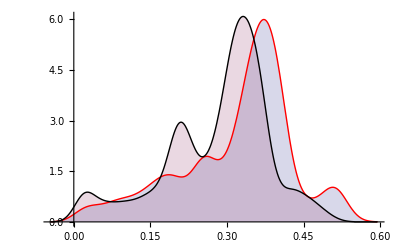

```mathematica
SmoothHistogram[
Table[Annotation[apByMethod[[i,2]],apByMethod[[i,1]],"Mouse"],{i,1,Length[apByMethod]}]
,Automatic,PlotStyle->styles,Filling->Bottom]
Dynamic[MouseAnnotation[]]
```

## Mean F1 score at fixed cut-of values

```mathematica
Table[{relevant[[1,i]],{"prec",i+1,"reC",i+2}},{i,Range[10,75,3]}]//MatrixForm
```

(1 | {prec,11,reC,12}
51 | {prec,14,reC,15}
101 | {prec,17,reC,18}
151 | {prec,20,reC,21}
201 | {prec,23,reC,24}
251 | {prec,26,reC,27}
301 | {prec,29,reC,30}
351 | {prec,32,reC,33}
401 | {prec,35,reC,36}
451 | {prec,38,reC,39}
501 | {prec,41,reC,42}
551 | {prec,44,reC,45}
601 | {prec,47,reC,48}
651 | {prec,50,reC,51}
701 | {prec,53,reC,54}
751 | {prec,56,reC,57}
801 | {prec,59,reC,60}
851 | {prec,62,reC,63}
901 | {prec,65,reC,66}
951 | {prec,68,reC,69}
1001 | {prec,71,reC,72}
1051 | {prec,74,reC,75})

We cut at 150 documents

```mathematica
precI=20;recI=21;
f1scores={#[[3;;]],If[#[[1]]+#[[2]]==0,0,(2*#[[1]]*#[[2]])/(#[[1]]+#[[2]])]}&/@relevant[[All,{precI,recI,8,9,1,2,3}]];
byMeth=GatherBy[f1scores,#[[1,{1,2,3,4,5}]]&];
f1ByMeth=Table[byMeth[[i,1,1]]-> Mean[Select[byMeth[[i,All,2]],#≠0&]],{i,1,Length[byMeth]}];
SortBy[f1ByMeth,#[[2]]&]//MatrixForm
```

({XAP,100,True,False,True}→0.353516
{LSI,500,True,False,True}→0.400214)

{RGBColor[1,0,0],GrayLevel[0]}

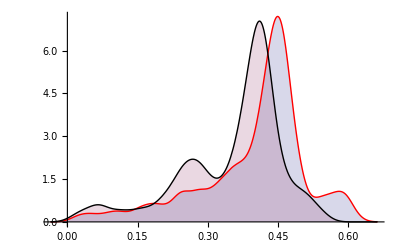

```mathematica
styles=Switch[#[[1,1,{1,2}]],{"XAP",100},Black,{"LSI",500},Red,{"LSI",250},Orange,{"LSI",750},{Red,Thick,Dashed},{"LSI",100},{Red,Dashed}]&/@ byMeth
SmoothHistogram[
Table[Annotation[
Select[byMeth[[i,All,2]],#≠0&],
byMeth[[i,1,1]],"Mouse"],{i,1,Length[byMeth]}]
,Automatic,PlotStyle->styles,Filling->Bottom]
Dynamic[MouseAnnotation[]]
```

## Comparing AP distributions with the T-test

```mathematica
byMethod=GatherBy [relevant,#[[{8,9,1,2,3}]]&];
apByMethod={#[[1,{8,9,1,2,3}]],Ap /@ #}& /@ byMethod;
apByMethod=Sort[apByMethod];
```

```mathematica
SortBy[{#[[1]],Mean[#[[2]]]}&/@ apByMethod,#[[2]]&]//MatrixForm
```

({XAP,100,True,False,True} | 0.283069
{LSI,500,True,False,True} | 0.319625)

```mathematica
sortedApByMethod=SortBy[apByMethod,Mean[#[[2]]]&];
```

```mathematica
Table[Prepend[sortedApByMethod[[i,1]],i],{i,1,Length[sortedApByMethod]}]//MatrixForm
```

(1 | XAP | 100 | True | False | True
2 | LSI | 500 | True | False | True)

```mathematica
TTest[{apByMethod[[1,2]],apByMethod[[2,2]]},Automatic,{"TestDataTable","ShortTestConclusion","TestConclusion"}]
```

TTest::nortst: At least one of the p-values in {0., 0.}, resulting from a test for normality, is below 0.025. The tests in {"T"} require that the data is normally distributed.

General::stop: Further output of TTest :: nortst will be suppressed during this calculation.

Intersection::normal: Nonatomic expression expected at position 2 in {"PairedT", "T", "Z", "KSampleT"} ∩ "T".

{ | Statistic | P-Value
T | 11.3664 | 1.52978×10^-29,Reject,The null hypothesis that the median difference is 0 is rejected at the 5. percent level based on the T test.}